# Optical Time Algorithm (OTA) | User-friendly playground to compute optical parameters

^1Mauro D’Achille, ^1Martin Gärttner, and ^(2,3)Tobias Haas

^1Institute of Condensed Matter Theory and Optics, Friedrich-Schiller-University Jena, Max-Wien-Platz 1, 07743 Jena, Germany
^2Institut für Theoretische Physik and IQST, Universität Ulm, Albert-Einstein-Allee 11, 89069 Ulm, Germany
^3Centre for Quantum Information and Communication, École polytechnique de Bruxelles, CP 165, Université libre de Bruxelles, 1050 Brussels, Belgium

Here, we provide a script to perform the Optical Time Algorithm (OTA) presented in the manuscript “Configurable photonic simulator for quantum field dynamics” for any positive definite Hamiltonian matrix which is block-diagonal with commuting blocks.

Information and Instructions

The notebook is auto-run and structured as follows:

Definitions and options: We define the beam splitter matrix consistently with the one presented in the paper.

OTA function: This section contains the definition of the function - named OTA - performing (numerically) the Optical Time Algorithm described in the paper and its only input is the Hamiltonian matrix (the function will check automatically that such a matrix satisfies the required properties for the OTA to hold). The output of this function is a table containing all the physical parameters needed to realize the optical circuit, i.e. the parameters for the phase shifters {d_j}, squeezers {z_j}and beam splitters {θ_ij}.

Playground: We provide, as an example, the fractional Laplacian Hamiltonian discussed in the paper (together with a pictorial representation of the optical circuit for 5 modes).
Feel free to play with all the (physical) parameters entering the game, namely the mass m, the lattice spacing ϵ and the interaction strength α. 
Notice that the computational time of this OTA function scales as a power law in the number of modes, as reported in the last plot, because of the way we implemented the iterative decomposition.

```mathematica
(* Evaluate here to run the notebook. *)
```

Definitions and Options

### Saving/Loading

```mathematica
(* Set directory to the notebook directory. *)
SetDirectory[NotebookDirectory[]];
```

### Definition of Beam Splitters (BS)

```mathematica
(* Define the two-mode beam splitter consistently with the definition given in the manuscript. *)
xpSBeamSplitter[θ_] := {{Cos[θ], Sin[θ], 0, 0}, {-Sin[θ], Cos[θ], 0, 0}, {0, 0, Cos[θ], Sin[θ]}, {0, 0, -Sin[θ], Cos[θ]}}

(* Define the generalized beam splitter needed for the iterative decomposition in the OTA. *)
GeneralxpSBeamSplitter[j_,k_, θ_, ModesNumber_]:= Table[If[y==j && z==j, xpSBeamSplitter[θ][[1,1]], 
If[y==j && z==k,  xpSBeamSplitter[θ][[1,2]],
If[y==k && z==j,  xpSBeamSplitter[θ][[2,1]],
If[y==k && z==k,  xpSBeamSplitter[θ][[2,2]],
If[y==j+ModesNumber && z==j+ModesNumber, xpSBeamSplitter[θ][[3,3]], 
If[y==j+ModesNumber && z==k+ModesNumber,  xpSBeamSplitter[θ][[3,4]],
If[y==k+ModesNumber && z==j+ModesNumber,  xpSBeamSplitter[θ][[4,3]],
If[y==k+ModesNumber && z==k+ModesNumber,  xpSBeamSplitter[θ][[4,4]],
IdentityMatrix[(2*ModesNumber)][[y,z]]]]]]]]]], 
{y, 1, (2*ModesNumber)}, {z, 1, (2*ModesNumber)}]
```

OTA function

```mathematica
(* OTA function. The only input is the Hamiltonian matrix.
Please notice that the ordering of the (symplectic) eigenvalues might differ with respect to the one visible in the manuscript.
For N=20, the estimated time for the computation is 5-6 seconds. *)
OTA[HamiltonianMatrix_]:= Module[
{ModesNumber, Hϕ,Hπ,
EigenValHϕ, EigenVecHϕ,EigenValHπ, EigenVecHπ,
gamma,SqueezerParameters,SymplecticEigenvalues,
NewEigenVec = {},
TallyFlag, PositionFlag,
deltaError=10^(-10),OrthogonalEigenVec,
BlockPN,rThetaSolFlag,GivensTable,
CompleteTable,ColumnList,CompleteDecomposition},

If[(Dimensions[HamiltonianMatrix][[1]]!=Dimensions[HamiltonianMatrix][[2]] ||OddQ[Dimensions[HamiltonianMatrix][[1]]]),
Print["Hamiltonian Matrix is not square with even dimension."],

(* Define ModesNumber. *)
ModesNumber=Dimensions[HamiltonianMatrix][[1]]/2;

If[(Not[PositiveDefiniteMatrixQ[HamiltonianMatrix]]||Chop[Im[HamiltonianMatrix]]!=ConstantArray[0,{2*ModesNumber,2*ModesNumber}]), 
Print["Hamiltonian Matrix not real and positive definite."], 
If[(Chop[HamiltonianMatrix[[1;;ModesNumber,ModesNumber+1;;2*ModesNumber]]]!=ConstantArray[0,{ModesNumber,ModesNumber}]||Chop[HamiltonianMatrix[[ModesNumber+1;;2*ModesNumber,1;;ModesNumber]]]!=ConstantArray[0,{ModesNumber,ModesNumber}]),
Print["The Hamiltonian matrix is not block diagonal."],

(* Define the two (commuting) blocks. *)
Hϕ = HamiltonianMatrix[[1;;ModesNumber,1;;ModesNumber]];
 Hπ =HamiltonianMatrix[[ModesNumber+1;;2*ModesNumber,ModesNumber+1;;2*ModesNumber]];

If[Chop[Hϕ.Hπ - Hπ.Hϕ]!=ConstantArray[0,{ModesNumber,ModesNumber}],
Print["The two blocks do not commute."],

(* Compute eigenvectors and eigenvalues of Hϕ and Hπ. *)
{EigenValHϕ, EigenVecHϕ} = Re[Eigensystem[Hϕ]];
{EigenValHπ, EigenVecHπ} = Re[Eigensystem[Hπ]];

(* Define the lists of squeezers and phases (symplectic eigenvalues). *)
gamma=Sqrt[EigenValHϕ/EigenValHπ];
SqueezerParameters=-Log[gamma]/2;
SymplecticEigenvalues = Sqrt[EigenValHϕ*EigenValHπ];

(* Orthogonal set of eigenvectors (in a given subspace with degenerate eigenvalues). The following routine needs around the same time as the N[] function but it is better in terms of the errors which produces over time. *)
TallyFlag = Tally[EigenValHϕ,Abs[#1-#2]<deltaError&];
For[i=1, i<=Length[TallyFlag], i++,
PositionFlag=Flatten[Position[EigenValHϕ,_?(Abs[#-TallyFlag[[i]][[1]]]<deltaError&)]];
If[TallyFlag[[i]][[2]]==1,
AppendTo[NewEigenVec, EigenVecHϕ[[PositionFlag[[1]]]]],
OrthogonalEigenVec = Orthogonalize[{EigenVecHϕ[[PositionFlag[[1]]]], EigenVecHϕ[[PositionFlag[[2]]]]}, Dot];
AppendTo[NewEigenVec,OrthogonalEigenVec[[1]]];
AppendTo[NewEigenVec, OrthogonalEigenVec[[2]]]]];

(********************************************************************************)
(* Define P given by the polar decomposition. *)
BlockPN = Chop[Normalize/@NewEigenVec];

(********************************************************************************)
(* Iterative decomposition of P (passive matrix after the polar decomposition in the manuscript).
Notice that a single mode phase shifter acting on the first or the last mode can be reabsorbed in the definition of the SSD without changing the squeezer layer by means of what is called gauge transformation in the manuscript. *)
Clear[k,j,rFlag,ThetaFlag];
GivensTable=Table[0,{i,ModesNumber},{j,ModesNumber}];

For[k=1,k<ModesNumber,k++,
For[j=k+1,j<=ModesNumber,j++,
If[BlockPN[[k,j]]!=0,
(* The following choice of sign and position in the matrix is due to our paper convention. See the minus sign in the second equation of the appendix! *)
rThetaSolFlag=Flatten[Quiet[NSolve[rFlag*Cos[ThetaFlag]==BlockPN[[k,k]]&&-rFlag*Sin[ThetaFlag]==BlockPN[[k,j]]&&rFlag>=0,{rFlag,ThetaFlag}]]]/.{C[1]->0};
BlockPN=Chop[BlockPN.(GeneralxpSBeamSplitter[k,j,ThetaFlag/.rThetaSolFlag[[2]], ModesNumber][[1;;ModesNumber,1;;ModesNumber]])];
GivensTable[[k,j]]=ThetaFlag/.rThetaSolFlag[[2]]]]];

(********************************************************************************)
(* Table preparation. *)
Clear[θ,d,z,i,j];
CompleteTable = Prepend[GivensTable,Range[ModesNumber]];
ColumnList=Join[{Subscript[θ,ij]}, Range[ModesNumber]];
CompleteTable=Transpose[Prepend[Transpose[CompleteTable],ColumnList]];
CompleteTable = Append[CompleteTable,Join[{Subscript[d,j]},SymplecticEigenvalues]];
CompleteTable = Append[CompleteTable,Join[{Subscript[z,j]},SqueezerParameters]];

CompleteDecomposition=Grid[CompleteTable, Frame->All]]]]]]
```

Playground

### Fractional Laplacian Hamiltonian

```mathematica
(* Hamiltonian matrix of the fractional Laplacian theory with periodic boundary condtions (PBC). *)
DiscreteFractionalHamiltonianMatrixPBC[ModesNumber_,α_,m_,ϵ_]:=Module[
{Hϕ,i,j,ϵps=N[ϵ](* To make it faster for integer inputs. *),HFL},
Hϕ=ConstantArray[0,{ModesNumber,ModesNumber}];
For[i=1,i<=ModesNumber,i++,
For[j=1,j<=ModesNumber,j++,
Hϕ[[i,j]]=
Sum[(1/ϵps)*Exp[-2*I*Pi*k*(i-j)/ModesNumber]*((2*Sin[π*k/ModesNumber])^α)/ModesNumber,{k,0,ModesNumber-1}]+ KroneckerDelta[i,j]*ϵps*m^α]];
(* Define the entire Hamiltonian matrix of interest, since Hπ is simply proportional to the identity. *)
HFL=ArrayFlatten[{{Simplify[Hϕ],0},{0,IdentityMatrix[ModesNumber]/ϵps}}]]
```

```mathematica
(* Relativistic case (α=2) for N=5 modes, mass m=1 and lattice spacing ϵ=2. *)
(* MatrixForm[DiscreteFractionalHamiltonianMatrixPBC[5,2,1,2.][[1;;5,1;;5]]] //Chop *)
```

```mathematica
(* Example for N=5 modes, α=2, mass m=1 and lattice spacing ϵ=2.
The θ parameters differ from the ones in the manuscript because of the different ordering of the eigenvalues. *)
OTA[DiscreteFractionalHamiltonianMatrixPBC[5,2,1,2.]]
```

θ_ij | 1 | 2 | 3 | 4 | 5
1 | 0 | 1.01722 | -0.704872 | 0.380891 | 0
2 | 0 | 0 | -2.22803 | 0.791708 | -0.684719
3 | 0 | 0 | 0 | 0.397177 | -0.955317
4 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0 | 0
d_j | 1.38004 | 1.38004 | 1.15995 | 1.15995 | 1.
z_j | -0.50763 | -0.50763 | -0.420763 | -0.420763 | -0.346574

#### Circuit representation for N = 5

Recall that a physical beam splitter (BS) is described by θ in [0, π/2], since its transmittivity is Cos^2[θ].
When θ is not in [0, π/2], one has two add two additional phase shifters of π: one on the first mode before the BS, and
1. one after the BS on mode two for θ in (π/2, π]$;
2. one before on mode two for θ in [-π, -π/2)$;
3. one after on mode one when θ in [-π/2, 0)$.

#### OPTIONAL: Run time analysis

```mathematica
(* Data generation of computational time vs number of modes. *)
(* dataTime=Table[{M,AbsoluteTiming[OTA[DiscreteFractionalHamiltonianMatrixPBC[M,2,1,2.]]][[1]]},{M,1,25}]; *)
```

Within our iterative decomposition, the computational time scales with the size as a power-law of exponent 2.51361.

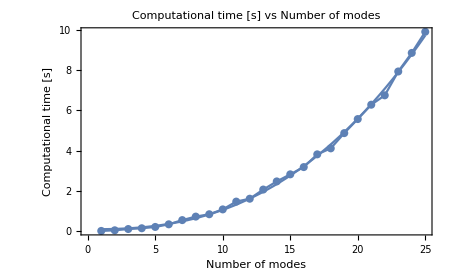

```mathematica
(* Computational time vs number of modes. *)
ComputationalTimeFit=FindFit[dataTime, a*x^b+c,{a,b,c},x];
Print["Within our iterative decomposition, the computational time scales with the size as a power-law of exponent "<>ToString[b/.ComputationalTimeFit]<>"."]
Show[ListPlot[dataTime,Joined->True,Mesh->All,FrameLabel->{"Number of modes","Computational time [s]"},BaseStyle->12,PlotLabel->Style["Computational time [s] vs Number of modes",FontSize->18, Black],Frame->True,ImageSize->450, FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None] ,
Plot[a*y^b+c/.{ComputationalTimeFit},{y,1,25}]]
```